# Making A Graph Of A Directory’s Contents

The classic pedagogical computer science tree traversal problem, implemented and visualized in Wolfram Language.

Andrew Wheeler, June 29,  2018

As a newcomer to Wolfram Language from programming languages like Python on C++, I quickly had to come to terms with the unique style of Wolfram. In order to be a truly WL tree traversal that could also visualize the graph of the trees it traversed, it would need to take full advantage of the language’s unique syntax and functionality.

## The Process

This graph constructor follows a very standard recursive depth-first technique using function definitions depending on type and number of arguments. Each step adds associations to a complete list of associations, which will be used as the list of edges when assembling the graph; likewise, each step adds to a full list of element names (directories and files) to be used as the list of vertices.

## Getting To The Base Cases

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

directoryGraph will run through directories and behaves according to given arguments, leading to the base case where s_String is a file:

```mathematica
directoryGraph[a_Association] :=Join @@ KeyValueMap[makeGraph, a]
directoryGraph[s_String, a_Association] := Join[Thread[s -> Keys[a]], makeGraph[a]]
directoryGraph[s_String,Null]:={}
```

## Visualization

Top level of the function makes a graph out of all the associations given from the lower levels. The resulting graph can presented and formatted as needed:

```mathematica
directoryGraph[s_String?DirectoryQ]:=
LayeredGraphPlot[makeGraph[<|FileNameTake@s -> FileSystemMap[Null&,s,Infinity]|>]]
```

Fair warning: running this on a directory with too many contents will run for a loooooong time.

The following code returns an output for whatever directory you are currently in, which for me usually is under Documents\\WolframDesktop. Check with:

```mathematica
Directory[]
```

And move to the desired directory with SetDirectory[path]. Evaluating SetDirectory[] with no argument will set the current working directory to your “home” directory. When I evaluate directoryGraph[] on my given directory, I end up with this layered graph:

```mathematica
directoryGraph[Directory[]]
```

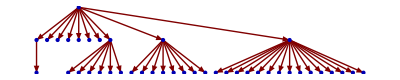

## Further explorations

A couple possible extensions to this representation would be to be able to move around the graph to see directories and their contents more clearly; the program could also be altered to only traverse to certain depths. Additionally, different graphing methods may be used, such as Graph instead of LayeredGraphPlot and the use of Style, but some default functionality of LayeredGraphPlot would be missed. Here are two representations of a larger directory tree, the first using Graph[] and the second using LayeredGraphPlot[]:

-Graphics-

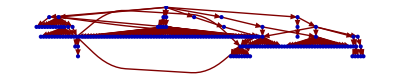

## Author contact information

axwheele@hamilton.edu